## Overview

This notebook acts as a companion to and generates the analysis of the paper: “Analysis of Activity Dependent Development of Topographic Maps in Neural Field Theory with Short Time Scale Dependent Plasticity”^1. In brief, we are interested in the role of Hebbian plasticity and spontaneously generated activity in the formation of a ubiquitous biological system: the topographic map. Current modelling of the role activity plays in the development of such systems is limited to assumptions of static activity input; a region of the receptive field of the post-synaptic region will be stimulated until equilibrium. The data generated by imaging experiments in mice show that the spontaneously generated activity comes in the form of propagating waves with complex spatio-temporal statistics. We then develop a framework in which the transient nature of these waves can be incorporated. In this notebook we will analyse the consequences and predictions of the model and examine how well the model can explain a key organisational feature of topographic maps: the width of the synaptic kernel. This is done by Markov-Chain-Monte-Carlo analysis.

#### Packages

This analysis will rely on a few dependencies coming both from Mathematica packages and a piece of custom software written by Josh Burkart to perform MCMC sampling^2. A slight modification to the package has been made to deal with boundary conditions that are not at infinity because we will be using uniform priors that terminate the sample space. The modification prevents the MCMC from attempting to sample outside of this space. We will load the native packages into Mathematica’s parallel framework but the MCMC functions will be imported to the parallel threads at a later time when those threads are initialized.

```mathematica
Needs["FourierSeries`"]
Needs["HypothesisTesting`"]
ParallelNeeds["FourierSeries`"]
ParallelNeeds["HypothesisTesting`"]
Get[FileNameJoin[{NotebookDirectory[],"mcmc.m"}]];
$Messages={};
```

Get::noopen: Cannot open /Users/nicholas_gale/Documents/University/2018 - 2021 (Ph.D)/Writing/11Thesis/Draft 10 - Revisions/nft_reanalysis/mcmc.m.

## Model

Here we will define the deterministic model derived from the analysis presented in the paper. This notebook will not detail the precise derivations that lead to the model; it is mainly concerned with the computational aspects of the paper and the generation of statistics which encapsulate biological descriptions and predictions. In brief, the model details the development of topographic maps which, in one dimension, can be characterised by a fundamental length referred to here as width. The model is developed quite generally but, as with all models, is not scientifically useful without comparison to data. The data we aim to predict comes from wild-type (genetically unaltered) and β2 (genetically altered) mice. The genetic alteration disrupts neural activity which the model is able to capture, and the phenotype of genetically altered mice increases the characteristic width of the organisation making these two references useful benchmarks for the model. By calibrating against the measurements we are able to make predictions about the effect of various biological mechanisms by interrogating the model.

Here we will also instantiate the common or default parameters that won' t change the estimate for the width of the topographic organisation which are primarily interested in. We should also keep in mind that while these parameters will not affect the prediction for the width they certainly affect other features of the kernel - the complete description of synaptic connections  in the system - and we do not claim that these are necessarily the correct parameters for our biological system of interest, simply that they will not affect the analysis.

#### Deterministic Model

```mathematica
(*A note about the scaling. The firing rate function modifies the connectivity kernel scaling by its derivative around the baseline firing rate. The activity functions are determined by the pre-synaptic field as is that connectivity scaling. These are equivalent in the model but they do not need to be. Therefore, the synaptic scaling is determined by whatever the pre-synaptic baseline scaling is squared: once for the pre-field activity,and once for the induced post-field activity. This allows us to elegantly subvert the fact that different fields have different firing rates by referring to the pre-field activity scaling alone and therefore scale according to the pertubation q_pre'(0) rather than confusingly have two firing rates: q(a) = a + q'(0)a*)
```

```mathematica
(* Firing rate *)
Q[rate_,v_,β_,t_]:=rate/(1+Exp[-β*(v-t)])
Q0[fr_,θ_,β_]:=Exp[θ*β]*fr*β/(1+Exp[θ*β])^2
preQ0=5;
(*Lateral Connectivity*)
W[x_,r1_,r2_,R1_]:=R1*r1 Exp[-1/2*x^2r1^2 ]-r2 Exp[-1/2*x^2r2^2];

(*Wave-Form*)
h[k_,s1_,s2_]:=s1 s2*Exp[-1/2*k^2*(s2)^2]

(*Non-Constant Part of FT{S}(k)*)
g[k_,c_,τ_,fr_,θ_,β_,tp_,r1_,r2_, R2_,u0_]:=4 c^2  k^2 τ Abs[tp]/(1+c^2k^2tp^2)/(c^2τ^2k^2+(1-Q0[fr,θ-u0,β]*W[k,r1,r2, R2])^2)

(*Fourier transform of the synaptic kernel*)
ftS[k_,κ_, λ_,τ_,τprime_,tp_,ap_,fr_,β_,θ_,s1_,s2_,c_,r1_,r2_,R1_,u0_] :=Re[ κ/λ(1/(1-g[k,c,τ,fr, θ,β,tp,r1,r2,R1,u0]*h[k,s1,s2]^2*ap^2*Q0[fr,θ-u0,β]*preQ0^2/λ) -1)]
ftSrenorm[k_,κ_, λ_,τ_,τprime_,tp_,ap_,fr_,β_,θ_,s1_,s2_,c_,r1_,r2_,R1_, u0_] :=Re[ κ/λ(1/(1-g[k,c,τ,fr, θ,β,tp,r1,r2,R1,u0]*h[k,s1,s2]^2*ap^2*Q0[fr,θ-u0,β]*preQ0^2/λ) -1)]-κ/λ

(*Synaptic Kernel*)
S[x_,κ_, λ_,τ_,τprime_,tp_,ap_,fr_,β_,θ_,s1_,s2_,c_,r1_,r2_,R1_,u0_]:=Re[NInverseFourierTransform[ftS[k,κ, λ,τ,τprime,tp,ap,fr,β,θ,s1,s2,c,r1,r2,R1,u0] ,k,x,Method->"GaussKronrodRule"]]
```

#### Parameters

Here we define default parameters which are used throughout the paper, and this notebook, unless otherwise specified.

```mathematica
κ=0.1;
λ=0.1;
ap=1;
β=0.26;
θ=-45;
s1=1;
fr=1;
τprime=100;
u0=-58;
```

#### Analysis Functions

Here we define two functions which will be useful for analysis: the width of the organisation, and the stability function. The organisation width is the predictor for the biological measurements made in the mouse superior colliculus retinotopic map. The stability function determines the points at which the model begins to exhibit singularities and therefore becomes inappropriate to explain biological data.

```mathematica
(*Width estimate*)
SWidth[τ_?NumericQ,tp_?NumericQ,s2_?NumericQ,c_?NumericQ,r1_?NumericQ,r2_?NumericQ,R1_?NumericQ]:=Abs[1/(10^-7+ArgMax[ftS[k,κ, λ,τ,τprime,tp,ap,fr,β,θ,s1,s2,c,r1,r2,R1,u0],k])]
(*SWidth[τ_?NumericQ,tp_?#<=0&,s2_?NumericQ,c_?NumericQ,r1_?NumericQ,r2_?NumericQ,R1_?NumericQ]:=10^9*)

(*Stability function*)
stab[k_,τ_?NumericQ,tp_?NumericQ,s2_?NumericQ,c_?NumericQ,r1_?NumericQ,r2_?NumericQ,R1_?NumericQ]:=g[k,c,τ,fr, θ,β,tp,r1,r2,R1,u0]*h[k,s1,s2]^2*ap^2*Q0[fr,θ-u0,β]*preQ0^2/λ
stabMax[τ_?NumericQ,tp_?NumericQ,s2_?NumericQ,c_?NumericQ,r1_?NumericQ,r2_?NumericQ,R1_?NumericQ]:=Max[stab[Table[k,{k,0.0,10,0.01}],τ,tp,s2,c,r1,r2,R1]]
```

#### Parameter Sensitivity

The model has several parameters which have various effects on model behaviour and predictions. A key predictor is the organisation width defined in the previous section which is sensitive only to a few parameters: it is invariant to all parameters chosen expect those in (∂g)/(∂k). The following widget allows informal exploration of the these parameters dependencies.

```mathematica
Manipulate[Plot[ftS[k,κ, λ,τ,τprime,tp,ap,fr,β,θ,s1,s2,c,r1,r2,R1,u0],{k,-1,1}],{{κ, 1},0,10}, {{λ, 1},0,10},{{τ, 1},0,10},{{τprime, 1},0,10},{{tp, 1},0,10},{{ap, 1},0,10},{{fr, 1},0,10},{{β, 1},0,10},{{θ, 1},-50,10},{{s1, 1},0,10},{{s2, 1},0,10},{{c, 1},0,10},{{r1, 1},0,10},{{r2, 1},0,10},{{R1, 1},0,10}, {{u0,0},-55,0}]
```

## Statistical Analysis

We would like to fit our model to a sample of wild-type mice and β2 mice. A reliable measurement of wave properties comes from Stafford et al (2009)^3. It is most appropriate to choose a measurement error model with categories of β2 and Wild-Type. In this section we are going to use an MCMC fitted model to regress on the data. We are choosing seconds as the time scale, and mm as the length scale. We will also need to estimate the parameters which dictate the recurrent kernel as this is not well studied.

#### Estimation of Recurrent Kernel

An essential feature of the model is the lateral or recurrent connections W. In mice there have been measurements of the extent to which the inhibitory and excitatory populations extend lengthwise in the superior colliculus; the post-synaptic target of interesting. We can estimate the data from the results shown in Figure 1 from Phongphanphanee et. al. (2014)^4. These data come in the form {location (μm), Maximal PSP}. We then perform a non-linear model fit on the ansatz form of these lateral connections commonly taken in the literature: the difference of two Gaussians. This informs a “best initial guess” of the parameters but we shall also estimate them via MCMC.

FittedModel[1.08248 ⅇ^(-30.082 x^2)-ⅇ^(-26.9677 x^2)]

| Estimate | Standard Error | Confidence Interval
R1est | 1.08248 | 0.010192 | {1.05418,1.11078}
r1est | 0.128923 | 0.012295 | {0.094787,0.16306}
r2est | 0.136164 | 0.0136187 | {0.0983525,0.173976}

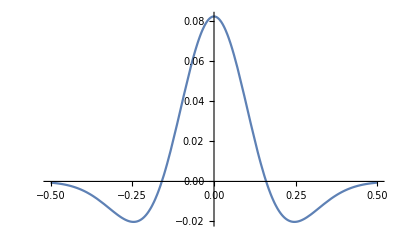

```mathematica
Fig1LM={{-450, -17.5}, {-300, -10},{-150, -20}, {0, 80}, {150, -5}, {300, -25}, {450, 0}};
Fig1RC ={{-450,-1}, {-300,1},{-150,40}, {0, 85}, {150, 5}, {300, -30}, {450, 10}};
dataAv = (Fig1LM + Fig1RC)/2;
data=Table[{dataAv[[i]][[1]]/1000,dataAv[[i]][[2]]/1000},{i,1,Length[dataAv]}];
model[x_,R1_,r1_,r2_]:=R1*Exp[-x^2/(2r1^2)]-Exp[-x^2/(2 r2^2)]
fit=NonlinearModelFit[data, model[x, R1est,r1est,r2est], {R1est,r1est,r2est},x]
fit["ParameterConfidenceIntervalTable"]
Plot[fit[x],{x,-0.5,0.5}]
```

#### Data

```mathematica
arboreasurements={{2.4*10^5,0.24*10^5},{8.9*10^5,0.93*10^5}};
wavespeedeasurements={{130.0, 15.0},{170.0, 30.0}};
wavelengthmeasurements={{225.0, 25.0},{400.0,25.0}};
```

We now do the necessary unit conversions to be appropriate for the model. We assume that the wave speed is measured in mm and therefore the area measurements should be scaled by a factor of ten so that s2 is also on the scale of millimeters.

```mathematica
areamicronstolengthmm[area_]:=Sqrt[(area)/Pi*10^-12]*10^3
lengthmicronstolengthmm[length_]:=length*10^-3
Npoints=Length[arboreasurements];
arborestimates=Table[{NormalDistribution,0.5*areamicronstolengthmm[arboreasurements[[i,1]]],0.5*areamicronstolengthmm[arboreasurements[[i,2]]] }, {i, 1, Npoints}];
s2estimates=Table[{NormalDistribution,0.5*lengthmicronstolengthmm[wavelengthmeasurements[[i,1]]],0.5*lengthmicronstolengthmm[wavelengthmeasurements[[i,2]]] }, {i, 1, Npoints}];
wavespeedestimates=Table[{NormalDistribution,lengthmicronstolengthmm[wavespeedeasurements[[i,1]]],lengthmicronstolengthmm[wavespeedeasurements[[i,2]]] }, {i, 1, Npoints}];
```

We can now define the likelihood function given a data point is from a particular category and under the assumption that the other parameters are independent of these particular mutations. Most of the parameters do not affect the size and can therefore be excluded, some of the parameters can be estimated (r1, r2) while others we attach an uninformative prior (τ, tp, R1). We start by defining the deterministic model, priors, and categorical likelihood. First make a convenience wrapper for all of the data.

```mathematica
estimates={arborestimates,s2estimates ,wavespeedestimates};
symfunction[j_,w_,s_,c_]:=If[j==1,w,If[j==2,s,If[j==3,c]]];
pdfdata[i_,estimates_,w_,s_,c_]:=Product[PDF[estimates[[j,i]][[1]][estimates[[j,i]][[2]], estimates[[j,i]][[3]]]][symfunction[j,w,s,c]],{j,1,Length[estimates]}]
```

#### Priors

Need to restrict these to the positive domain which is a problem for the MCMC package. Create a new PDF and use the HeavisideTheta function to get a functional evaluatable form for the MCMC package and then add a small perturbation to avoid a simplification by the WolframKernel.

```mathematica
pτ=Function[x, 1/(1-0.0001)*(HeavisideTheta[x-0.0001]-HeavisideTheta[x-1])];
ptp=Function[x, 1/(5-0.0001) *(HeavisideTheta[x-0.0001]-HeavisideTheta[x-5])];

(*Informative Priors*)
pR1=PDF[NormalDistribution[1.08,0.01]];
pr1=PDF[NormalDistribution[0.13,0.012]]; 
pr2 =PDF[NormalDistribution[0.14,0.014]];

Clear[pdf];
pdf[fun_]:=Simplify[Evaluate[fun[#]], #>0]*HeavisideTheta[#]&;
priorpdfs={pτ,ptp,pr1,pr2,pR1};
```

#### Likelihood Model

There are quite a few parameters so we shall assemble the likelihood in the following form: independent variables sampled from measurement distributions, likelihood of dependent variable under normal error assumption, and priors for parameters.

```mathematica
L[τ_,tp_,s2_,c_,r1_,r2_,R1_,estimates_,i_]:=pdfdata[i,estimates,SWidth[τ,tp,s2,c,r1,r2,R1],s2,c]*
pdf[pτ][τ]*pdf[pr1][r1]*pdf[pr2][r2]*pdf[pR1][R1]*pdf[ptp][tp]
```

Now we define the log-likelihood for all of the data. This is what we will be minimising via MCMC.

```mathematica
Clear[logL,loglikelihood,τ,tp,s2,c,r1,r2,R1]
logL[τ_,tp_,s2_,c_,r1_,r2_,R1_]:=Evaluate[Simplify[PowerExpand[Sum[Log[L[τ,tp,s2,c,r1,r2,R1,estimates,i]],{i,1,Npoints}]]]];
loglikelihood=Evaluate[logL[τ,tp,s2,c,r1,r2,R1]]
```

-12078.9+766.667 c-2777.78 c^2+1805.56 r1-6944.44 r1^2+21600. R1-10000. R1^2+1428.57 r2-5102.04 r2^2+2000. s2-6400. s2^2+2 Log[HeavisideTheta[r1]]+2 Log[HeavisideTheta[R1]]+2 Log[HeavisideTheta[r2]]+2 Log[-HeavisideTheta[-5+tp]+HeavisideTheta[-0.0001+tp]]+2 Log[HeavisideTheta[tp]]+2 Log[-HeavisideTheta[-1+τ]+HeavisideTheta[-0.0001+τ]]+2 Log[HeavisideTheta[τ]]+108.32 SWidth[τ,tp,s2,c,r1,r2,R1]-329.361 SWidth[τ,tp,s2,c,r1,r2,R1]^2

#### MCMC

Now we perform the MCMC giving it lots of room to breath. We need to check that the MCMC did converge which probably will entail running several chains and doing some convergence measures. We will do 8 chains corresponding to two initializations in each of the sample basins and run for 100000 trials. Once each of the chains are complete we compute the Rubin-Gelman statistic to see if the MCMC has converged and combine all of the parameter runs together. Then we can plot the distributions, time-series, histogram and pick most likely parameters on all parameters that haven’t been estimated from data. Whether any of these other parameters in the model correlate with these experimental categories remains to be seen, but as a reasonable judgement we are assuming that they are independent: β2  knock-out is probably not going to change the time scale on which plasticity occurs, for example.

```mathematica
Clear[res, pw]
SeedRandom[9876543210];
jumps=Re[0.25*Table[If[i≤Length[estimates]-1, estimates[[i+1]][[2]][[3]], Chop[Sqrt[Integrate[x^2 priorpdfs[[i-Length[estimates]+1]][x], {x,-∞,∞}] -Integrate[x priorpdfs[[i-Length[estimates]+1]][x] ,{x,-∞,∞}]^2]]],{i,1,7}]];
nchains=6;
domain =Reals;
ip=Table[(1+0.01*(RandomReal[]))*If[i≤Length[estimates]-1, estimates[[i+1]][[Mod[j-1,Npoints]+1]][[2]], ArgMax[priorpdfs[[i-Length[estimates]+1]][x],x]],{i,1,7},{j,1,nchains}];
ip=Table[(1+0.1*(RandomReal[]))*If[i≤Length[estimates]-1, estimates[[i+1]][[Mod[j-1,Npoints]+1]][[2]], Chop[Integrate[x priorpdfs[[i-Length[estimates]+1]][x] ,{x,-∞,∞}]]],{i,1,7},{j,1,nchains}];

ntrials=Round[10^5];
(*Generate a new test, or load an old one*)
generate=False;
(*Create a parallel worker*)
pw[j_,ntrials_,domain_, jumps_,ip_]:=Block[{τ,tp,s2,c,r1,r2,R1},$Messages={};
MCMC[loglikelihood,{{s2,ip[[1,j]],jumps[[1]],domain},
{c,ip[[2,j]],jumps[[2]],domain},
{τ,ip[[3,j]],jumps[[3]],domain},
{tp,ip[[4,j]],jumps[[4]],domain},
{r1,ip[[5,j]],jumps[[5]],domain},
{r2,ip[[6,j]],jumps[[6]],domain},
{R1,ip[[7,j]],jumps[[7]],domain}
},ntrials]]

DistributeDefinitions[pw];ParallelEvaluate[pw=pw;];
DistributeDefinitions[MCMC];ParallelEvaluate[MCMC=MCMC;];
Clear[mcmcrun,res];
```

```mathematica
AbsoluteTiming[If[generate,res=ParallelTable[pw[j,ntrials,domain,jumps,ip], {j,1,Dimensions[ip][[2]]}];
Table[mcmcrun[i]=res[[i]], {i,1,Dimensions[ip][[2]]}];
DeleteFile[NotebookDirectory[]<>"chains"<>".m"];
Save[NotebookDirectory[]<>"chains"<>".m",mcmcrun]];]
```

{2.×10^-6,Null}

```mathematica
(*collect results*)
Get[NotebookDirectory[]<>"chains"<>".m"];
```

#### Generate the Gelman-Rubin convergence diagnostic

```mathematica
(*generate the entire posterior over all chains for each parameter*)
posterior=Table[Flatten[Join[Table[mcmcrun[i]["ParameterRun"][[1;;ntrials,j ]], {i,1,nchains}]]],{j,1,Length[mcmcrun[1]["Parameters"]]}];
(*generate chain means and variances *)
chainmeans= Table[Mean[mcmcrun[i]["ParameterRun"][[1;;ntrials,j ]]], {i,1,nchains},{j,1,Length[mcmcrun[1]["Parameters"]]}];
chainvariance= Table[Variance[mcmcrun[i]["ParameterRun"][[1;;ntrials,j ]]], {i,1,nchains},{j,1,Length[mcmcrun[1]["Parameters"]]}];

(*calculate the Between Chain and Within Chain variances for each parameter*)
Bvar=Table[ntrials/(nchains-1)*Sum[(chainmeans[[i,j]]-Mean[chainmeans[[All,j]]])^2,{i,1,nchains}],{j,1,Length[mcmcrun[1]["Parameters"]]}];
Wvar=Table[Mean[chainvariance[[All,j]]],{j,1,Length[mcmcrun[1]["Parameters"]]}];

(*Caculate the pooled variance and the PRSF*)
Vbar=(ntrials-1)/ntrials * Wvar +( nchains+1)/(ntrials*nchains)*Bvar;
PRSF=Sqrt[Vbar/Wvar]
```

{1.00011,1.0001,1.00023,1.00026,1.0001,1.00037,1.00018}

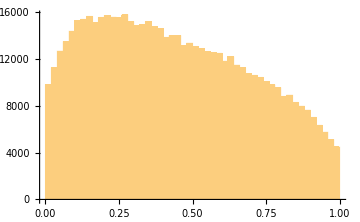
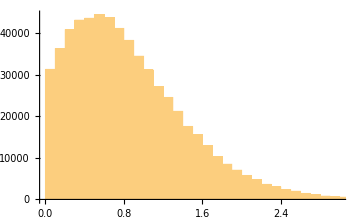
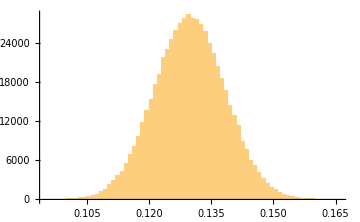
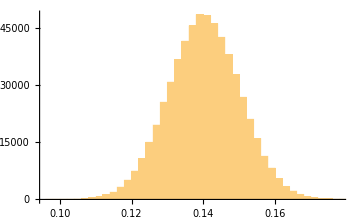
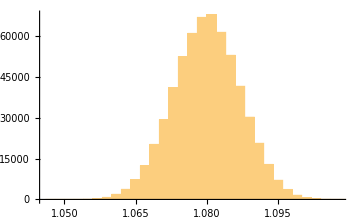

```mathematica
nbins=50;
Table[Histogram[posterior[[i]], nbins, ImageSize->Medium], {i,3,Length[posterior]}]
```

#### Goodness of Fit

We need to establish a goodness of fit for our model. While there are always a number of potential issues concerning model fits for our purposes we shall simply calculate the R2 coefficient.

```mathematica
(*find the best fit*)
findmaxlikelihoodhistogram[data_,b_]:=Block[{counts,bins,binIdx,max}, {bins,counts}=HistogramList[data,b];binIdx=Position[counts,Max[counts]][[1]][[1]];max=bins[[binIdx]];max*1.0];
findmaxlikelihood[posterior_]:=Block[{dist,x}, dist=PDF[SmoothKernelDistribution[posterior]];x/. FindMaximum[dist[x],{x,findmaxlikelihoodhistogram[posterior,nbins]}][[2]]];
bestfit=Table[findmaxlikelihood[posterior[[j]]],{j,1,Dimensions[ip][[1]]}];
params=bestfit[[3;;Length[bestfit]]];
model[s2_,c_]:=Evaluate[SWidth[#1, #2,s2,c,#3,#4,#5]&@@params];
```

```mathematica
Print["Data"]
modelpredictors=1.0*Table[model[estimates[[2]][[i]][[2]],estimates[[3]][[i]][[2]]],{i,1,Npoints}]
widthdata=Table[estimates[[1]][[i]][[2]],{i,1,Npoints}]
widthvar=Table[estimates[[1]][[i]][[3]],{i,1,Npoints}]^2;
weights=Table[1/estimates[[1]][[i]][[3]]^2,{i,1,Npoints}];
Print["Variance"]
modelvariance=Total[(modelpredictors-widthdata)^2]/Length[widthdata]
datavariance=Total[(widthdata-Mean[widthdata])^2]/Length[widthdata]
weighteddatavariance=Total[(widthdata-Total[widthdata*weights]/Total[weights])^2]/Length[widthdata];
Print["Fit"]
R2=1-modelvariance/weighteddatavariance
R2=1-modelvariance/datavariance;
```

Data

{0.132194,0.221104}

{0.138198,0.266128}

Variance

0.00103157

0.00409152

Fit

0.812937

## Image Generation

In this section we want to generate the images that guide the paper. We will define some global plotting parameters and in each subsection highlight any plot specific parameters.

```mathematica
textsize=20;
titlesize=25;
imsize={600,500};
```

### Model Summary

This is the hardest figure to do programmatically as it required many changes on the basis of input from several different people. As a result the most straightforward, albeit not very reproducible, method to create the image was to generate four individual graphics and use the Mathematica image editing tool to arrange them. The graphics consist of a base summary image of the model and three additional images containing information about various aspects of the model which are overlain over the base image. The code for generating the separate graphics is shown below and the final edited image is presented in a single cell.

```mathematica
(*Plotting parameters*)
textsizebase=29;

(*Plot base summary*)
gmodel=GraphPlot[{
{1->1,Style["Recurrent Connections: W(x, x')",textsize]},
{2->1,Style["Feed Foward Connections: S(x, y, T)", textsizebase]}
},
VertexLabels->{
1-> Placed[{Style["Post-Synaptic Activity: \n u(x,t)", textsize, Italic]},Center],
 2->Placed[{Style["Pre-Synaptic Activity: \n a(y,t)",textsizebase, Italic]},Center]
}, 

VertexSize->0.5,
VertexShapeFunction->"Circle" ,
VertexCoordinates->{1->{0.5,0.0},2->{0,0.5}},
EdgeWeight->{1,20},
GraphLayout->{"SpringElectricalEmbedding"},
ImageSize->{1000,1000}];

(*Plot overlay images*)
act=Graphics[Plot[Exp[-x^2], {x,-2,2},ImageSize->300,AxesLabel->{Style["(y-ct)", textsize],Style["a(y,t)", textsize]},Ticks->None,Epilog->Inset[Graphics[{Red,Thick,Arrowheads[Large],Arrow[{{0.0,1}, {0.5, 1.0}}]}], {0.5,1}]]];
act=Graphics[Plot[Exp[-4x^2], {x,-2,2},PlotStyle->Orange,ImageSize->300,AxesLabel->{Style["(x-ct)", textsize],Style["u(x,t)", textsize]},Ticks->None,Epilog->Inset[Graphics[{Red,Thick,Arrowheads[Large],Arrow[{{0.0, 1}, {0.5, 1.0}}]}], {0.5,1}]]];
lat=Graphics[Plot[Exp[-x^2]-1/1.5*Exp[-1/2*x^2], {x,-4,4},PlotStyle->Purple,ImageSize->Medium,AxesLabel->{Style["(x-x')", textsize],Style["W(x,x')", textsize]},Ticks->None,Epilog->Inset[Graphics[{Red,Thick,Arrowheads[Large],Arrow[{{0.0, 1}, {1.0, 1.0}}]}], {0.6,1}]]];
```

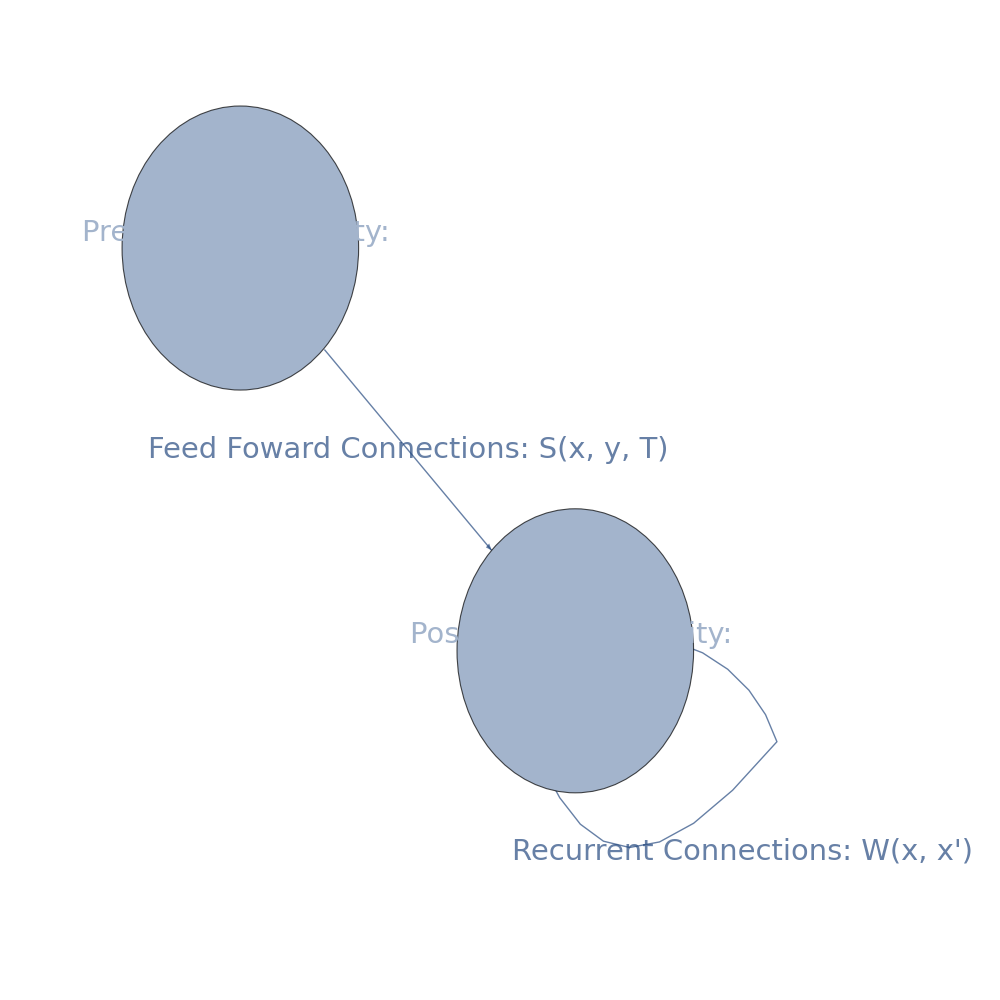

-Graphics-

### Retinotopy

```mathematica
(*Plot specific functions*)
LateralConnectionsCurvilinear[x_,y_]:=2*Exp[- Abs[(x-y^3)]]-1*Exp[-Abs[ (x-y^3)/2]]
LateralConnectionsLinear[x_,y_]:=2*Exp[- Abs[(x-y)]]-1*Exp[-Abs[ (x-y)/2]]
```

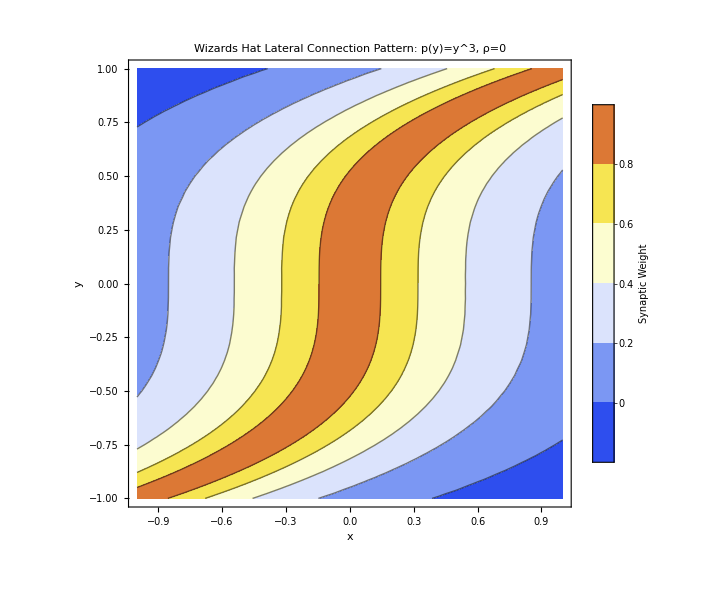

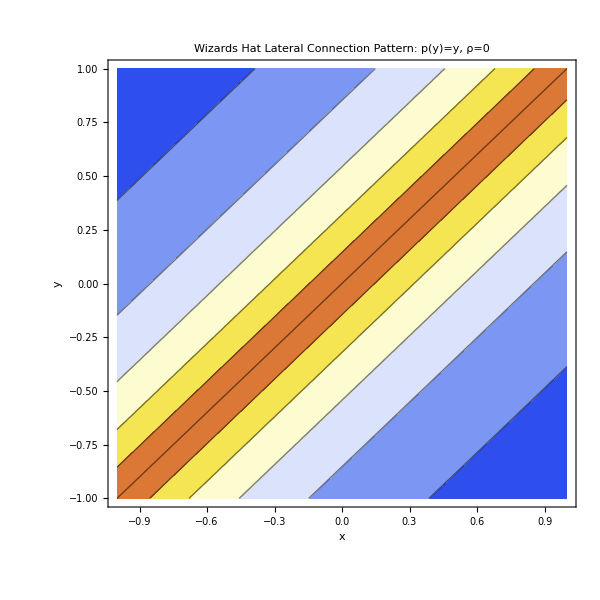

```mathematica
(*Plots*)
ContourPlot[
LateralConnectionsCurvilinear[x,y],{x,-1,1},{y,-1,1},
ColorFunction->"TemperatureMap",
PlotLabel->Style["Wizards Hat Lateral Connection Pattern: \n p(y)=y^3, ρ=0", "Section", titlesize], 
FrameTicksStyle->Directive["Label", textsize],
FrameLabel->{Style["x", Bold, textsize],Style["y", Bold, textsize]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize->200,LegendMargins->2,LegendLabel->Style["Synaptic \n Weight",textsize]],
ImageSize->imsize]

ContourPlot[
LateralConnectionsLinear[x,y],{x,-1,1},{y,-1,1},
ColorFunction->"TemperatureMap",
PlotLabel->Style["Wizards Hat Lateral Connection Pattern: \n p(y)=y, ρ=0", "Section", titlesize],
FrameTicksStyle->Directive["Label", textsize],
FrameLabel->{Style["x", Bold, textsize],Style["y", Bold, textsize]},
ImageSize->imsize
]
```

### Typical Organisations

```mathematica
(*Biological parameters*)
τ = 0.1;tp = 1.0;s2 = 0.1;c = 0.1;r1 = 0.129;r2 = 0.136;R1 = 1.078;
```

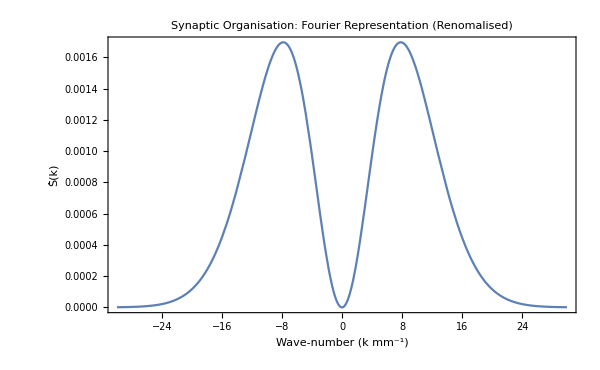

-Graphics-

```mathematica
(*Plots*)
Plot[ftS[k,κ, λ,τ,τprime,tp,ap,fr,β,θ,s1,s2,c,r1,r2,R1,u0], {k, -30,30}, PlotRange->All, PlotLabel->Style["Synaptic Organisation: \n Fourier Representation (Renomalised)", "Section", titlesize], Axes->False,Frame->{True,True, False,False},FrameLabel->{Style["Wave-number (k mm^-1)", textsize, Black], Style["Ŝ(k)",textsize, Black]} ,ImageSize->imsize, FrameStyle->Directive["Label", textsize]]

Quiet[Plot[S[x,κ, λ,τ,τprime,tp,ap,fr,β,θ,s1,s2,c,r1,r2,R1, u0], {x, -1,1}, PlotRange->All,PlotLabel->Style["Synaptic Organisation: \n Real Representation (Renormalised)", "Section", titlesize], Axes->False,Frame->{True,True, False,False},FrameLabel->{Style["Distance (x mm)", textsize, Black],Style[ "S(x)",textsize, Black]} ,ImageSize->imsize, FrameStyle->Directive["Label", textsize]]]
```

### Stability Surface

```mathematica
(*Plot parameters and functions*)
axismin=0.0;
axismax=10.0;
stabpos={1.05,0.20};

regionfunction=Evaluate[Max[stab[Table[k,{k,0,10,0.01}],c,r,s]]/.{c->#1,r->#2,s->#3}]&;
regionfunction=Evaluate[Max[stab[Table[k,{k,0,10,0.01}],c,r,s]]/.{c->#1,r->#2,s->#3}]&;
regioncap=1.01;
```

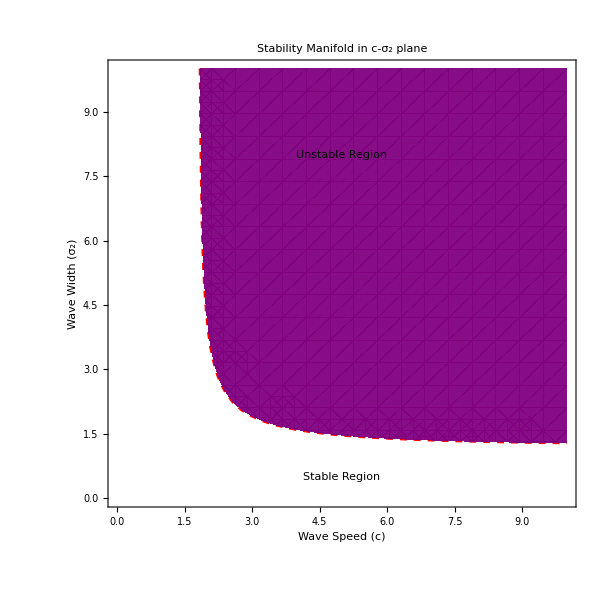

```mathematica
(*Stability surface*)
Show[

ContourPlot[stabMax[τ,tp,s2,c,r1,r2,R1]==1, {c,axismin,axismax},{s2,axismin,axismax},
AxesOrigin->{axismin,axismin},
FrameLabel->{Style["Wave Speed (c)", Bold, textsize],Style["Wave Width (σ_2)", Bold, textsize]},
PlotLabel->Style["Stability Manifold in c-σ_2 plane", "Section", titlesize],
Mesh->None,
ContourStyle->Directive[Red,Dashed,Bold],
FrameTicksStyle->Directive[textsize],
ImageSize->imsize
],

RegionPlot[stabMax[τ,tp,s2,c,r1,r2,R1]>regioncap,{c,axismin,axismax},{s2,axismin,axismax},
BoundaryStyle->None,PlotStyle->Directive[Opacity[0.95],Purple],
ImageSize->imsize],

Epilog->{
Inset[Framed[Style["Unstable Region",20],Background->White],{5,8}],
Inset[Framed[Style["Stable Region",20],Background->White],{5,0.5}]
}
]
```

### Width, and Amplitudes

```mathematica
(*Plot parameters*)
barpos={1.05,0.5};
legendmarker =360;
legendmargins=2;

axismin=0.001;
cmax=1.0;
s2max=1.0;
τmax=1.0;
tpmax=5.0;
r1max=1.0;
r2max=0.5;
Rmax=1.0;
```

```mathematica
ContourPlot[SWidth[τ,tp,s2,c,r1,r2,R1] ,{c,axismin,cmax},{s2,axismin,s2max},
PlotLabel->Style[StringForm["Synaptic Organisation Width: c-σ_2 plane"], "Section", titlesize],
FrameLabel->{Style["Wave Speed (c)", Bold, textsize],Style["Wave Width (σ_2)", Bold, textsize]},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->legendmarker,LegendMargins->legendmargins,LegendLabel->Style["Ω",textsize]],barpos],
FrameTicksStyle->Directive[textsize],
ImageSize->imsize]

ContourPlot[SWidth[τ,tp,s2,c,r1,r2,R1] ,{τ,axismin,τmax},{tp,axismin,tpmax},
PlotLabel->Style[StringForm["Synaptic Organisation Width: τ-t_p plane"], "Section", titlesize],
FrameLabel->{Style["Activity Time Scale (τ)", Bold, textsize],Style["Plasticity Window (t_p)", Bold, textsize]},
FrameTicksStyle->Directive[textsize],
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->legendmarker,LegendMargins->legendmargins,LegendLabel->Style["Ω",textsize]],barpos],
ImageSize->imsize]

ContourPlot[SWidth[τ,tp,s2,c,r1,r2,R1] ,{r1,axismin,0.5 * r1max},{r2,axismin,r2max},
PlotLabel->Style[StringForm["Synaptic Organisation Width: r_1-r_2 plane"], "Section", titlesize],
FrameLabel->{Style["Recurrent Excitation Length (r_1)", Bold, textsize],Style["Recurrent Inhibition Length (r_2)", Bold, textsize]},
FrameTicksStyle->Directive[textsize],
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->legendmarker,LegendMargins->legendmargins,LegendLabel->Style["Ω",textsize]],barpos],
ImageSize->imsize]

ContourPlot[SWidth[τ,tp,s2,c,r1,r2,R1] ,{R1,axismin,Rmax},{r1,axismin,r1max},
PlotLabel->Style[StringForm["Synaptic Organisation Width: R_1-r_1 plane"], "Section", titlesize],
FrameLabel->{Style["Recurrent Amplitude (R_1)", Bold, textsize],Style["Reccurent Excitation Scale (r_1)", Bold, textsize]},
FrameTicksStyle->Directive[textsize],
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->legendmarker,LegendMargins->legendmargins,LegendLabel->Style["Ω",textsize]],barpos],
ImageSize->imsize]
```

-Graphics-

-Graphics-

-Graphics-

ContourPlot[SWidth[τ,tp,s2,c,r1,r2,R1],{R1,axismin,rmax},{r1,axismin,r1max},PlotLabel→Synaptic Organisation Width: R_1-r_1 plane,FrameLabel→{Recurrent Amplitude (R_1),Reccurent Excitation Scale (r_1)},FrameTicksStyle→Directive[textsize],PlotLegends→Placed[BarLegend[Automatic,LegendMarkerSize→legendmarker,LegendMargins→legendmargins,LegendLabel→Ω],barpos],ImageSize→imsize]

### Posteriors

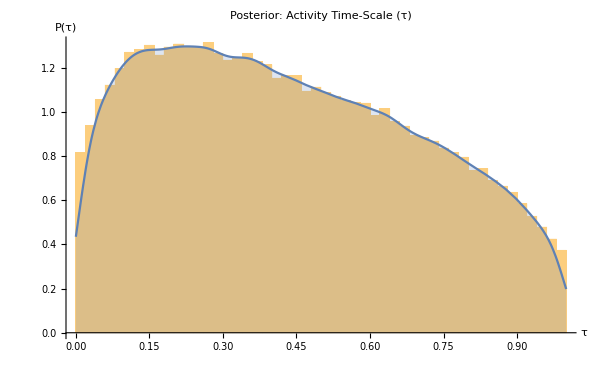

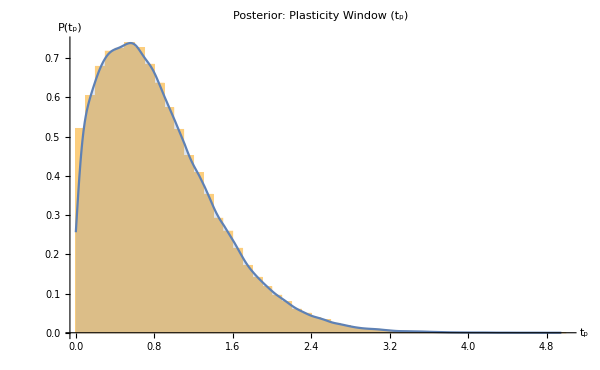

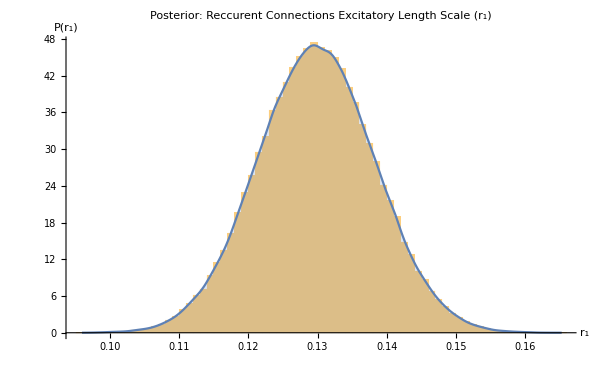

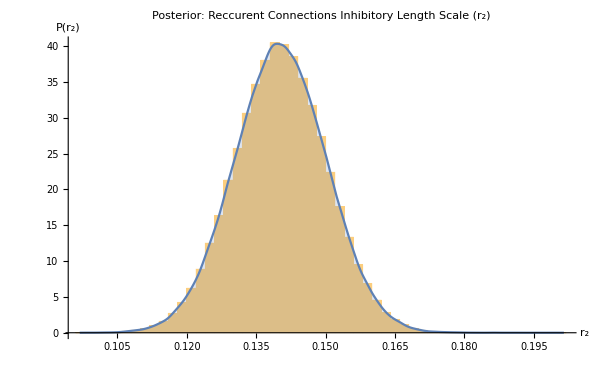

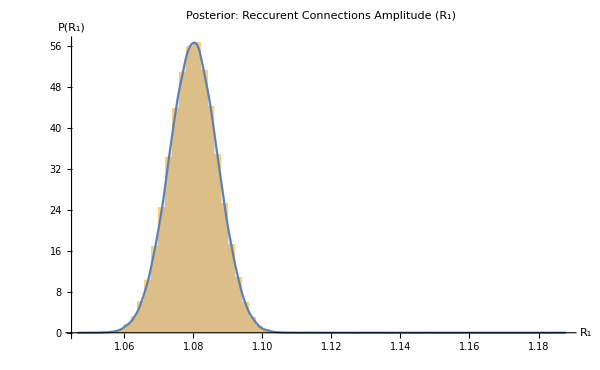

```mathematica
imtext=16;
sectext=22;
Show[Histogram[posterior[[3]], 50, "ProbabilityDensity"], Plot[PDF[SmoothKernelDistribution[posterior[[3]]]][x],{x,Min[posterior[[3]]],Max[posterior[[3]]]}, Filling->Axis,PlotRange->{0,All}],ImageSize->imsize,PlotRange->All, PlotLabel->Style[StringForm["Posterior: Activity Time-Scale (τ)"], "Section", titlesize],
 TicksStyle->Directive["Label", textsize],
AxesLabel->{Style["τ", Bold, textsize],Style["P(τ)", Bold, textsize]}]
Show[Histogram[posterior[[4]], 50, "ProbabilityDensity"], Plot[PDF[SmoothKernelDistribution[posterior[[4]]]][x],{x,Min[posterior[[4]]],Max[posterior[[4]]]}, Filling->Axis,PlotRange->{0,All}],ImageSize->imsize,PlotRange->All, PlotLabel->Style[StringForm["Posterior: Plasticity Window (t_p)"], "Section", titlesize],
 TicksStyle->Directive["Label", textsize],
AxesLabel->{Style["t_p", Bold, textsize],Style["P(t_p)", Bold, textsize]}]
Show[Histogram[posterior[[5]], 50, "ProbabilityDensity"], Plot[PDF[SmoothKernelDistribution[posterior[[5]]]][x],{x,Min[posterior[[5]]],Max[posterior[[5]]]}, Filling->Axis,PlotRange->{0,All}],ImageSize->imsize,PlotRange->All, PlotLabel->Style[StringForm["Posterior: Reccurent Connections Excitatory Length Scale (r_1)"], "Section", titlesize],
 TicksStyle->Directive["Label", textsize],
AxesLabel->{Style["r_1", Bold, textsize],Style["P(r_1)", Bold, textsize]}]
Show[Histogram[posterior[[6]], 50, "ProbabilityDensity"], Plot[PDF[SmoothKernelDistribution[posterior[[6]]]][x],{x,Min[posterior[[6]]],Max[posterior[[6]]]}, Filling->Axis,PlotRange->{0,All}],ImageSize->imsize,PlotRange->All, PlotLabel->Style[StringForm["Posterior: Reccurent Connections Inhibitory Length Scale (r_2)"], "Section", titlesize],
 TicksStyle->Directive["Label", textsize],
AxesLabel->{Style["r_2", Bold, textsize],Style["P(r_2)", Bold, textsize]}]
Show[Histogram[posterior[[7]], 50, "ProbabilityDensity"], Plot[PDF[SmoothKernelDistribution[posterior[[7]]]][x],{x,Min[posterior[[7]]],Max[posterior[[7]]]}, Filling->Axis,PlotRange->{0,All}],ImageSize->imsize,PlotRange->All, PlotLabel->Style[StringForm["Posterior: Reccurent Connections Amplitude (R_1)"], "Section", titlesize],
 TicksStyle->Directive["Label", textsize],
AxesLabel->{Style["R_1", Bold, textsize],Style["P(R_1)", Bold, textsize]}]
```

## References

1. Gale, N., Rodger, J., Small, M. & Eglen, S. Analysis of activity dependent development of topographic maps in neural field theory with short time scale dependent plasticity. Mathematical Neuroscience and Applications 2, (2022)
2. J. Burkart. Mathematica Markov chain Monte Carlo. https://github.com/joshburkart/mathematica-mcmc, (2017)
3. Stafford, B. K., Sher, A., Litke, A. M. & Feldheim, D. A. Spatial-temporal patterns of retinal waves underlying activity-dependent refinement of retinofugal projections. Neuron 64, 200–212 (2009)
4. Phongphanphanee, P. et al. Distinct local circuit properties of the superficial and intermediate layers of the rodent superior colliculus. Eur. J. Neurosci. 40, 2329–2343 (2014)